# Sección De Poincaré

La sección de Poincaré nos permite visualizar a complejidad de la dinámica de cierto tipo de sistemas. Consiste en realizar un corte de una sección en el espacio de fases de manera que se maximice la cantidad de información.

## Del oscilador de Duffing

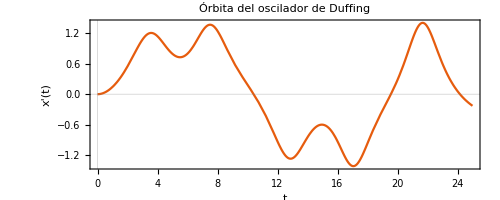

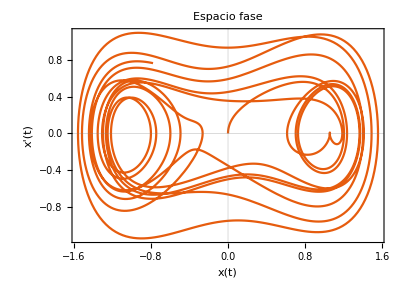

```mathematica
sol=Block[{δ=0.15,γ=0.3,x},
NDSolve[
{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0},x,{t,0,100},MaxSteps->∞
]
][[1,1]];

ParametricPlot[Evaluate[{t,x[t]}/.sol],{t,0,25},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"t","x'(t)"},PlotLabel->"Órbita del oscilador de Duffing"]
ParametricPlot[Evaluate[{x[t],x'[t]}/.sol],{t,0,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"x(t)","x'(t)"},PlotLabel->"Espacio fase"]
```

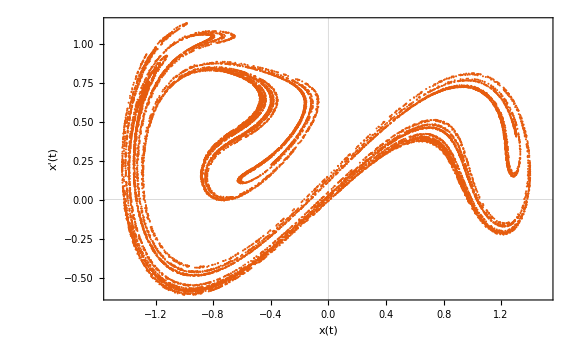

```mathematica
poincare=Block[{δ=0.15,γ=0.3,x},
Reap[
NDSolve[
{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0,WhenEvent[Mod[t,2π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞
]
]
][[-1,1]];
ListPlot[poincare,ImageSize->Large,PlotRange->{{-1.5,1.5},All},PlotStyle->PointSize[0.0025],FrameLabel->{"x(t)","x'(t)"},PlotTheme->"Scientific"]
```

## Del problema de 3 cuerpos restringido

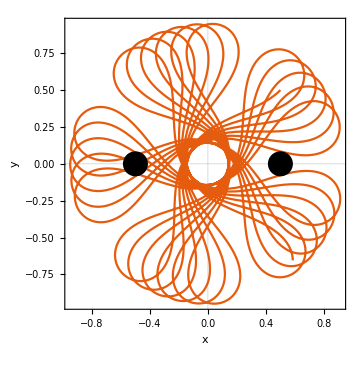

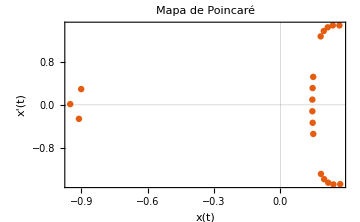

```mathematica
x0 = 0.5; y0 = 0.5;
vx0 = -0.5; vy0 = -0.5;

sol=Block[{μ = 1, x, y},
NDSolve[
{
x''[t]==2 y'[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
y''[t]==-2 x'[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==x0,y[0]==y0,
x'[0]==vx0,y'[0]==vy0},
{x,y},{t,0,70}
]
];

puntos=Block[{μ = 1, x, y},
Reap[
NDSolve[
{
x''[t]==2 y'[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
y''[t]==-2 x'[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==x0,y[0]==y0,
x'[0]==vx0,y'[0]==vy0,
WhenEvent[y[t] == 0 && y'[t] > 0,Sow[{x[t],x'[t]}]]
},
{x,y},{t,0,70}
]
]
];
Show[
ParametricPlot[{x[t],y[t]} /. sol,{t,0,70},PlotTheme->"Scientific",FrameLabel->{"x","y"},BaseStyle->FontSize->14],
ListPlot[{{-0.5,0},{0.5,0}},PlotStyle->{PointSize[0.05],Black},PlotTheme->"Scientific"]
]

ListPlot[puntos[[2,1]],ImageSize->Medium,PlotTheme->"Scientific", FrameLabel->{"x(t)","x'(t)"}, PlotLabel->"Mapa de Poincaré",PlotRange->Full]
```